# EllipticIntegrals Paclet Examples

This notebook demonstrates how to load and use the ArnoudBuzing/EllipticIntegrals paclet.

## Loading the Paclet

First, ensure the paclet is loaded in your Wolfram Language session. We load it using the directory path:

```mathematica
(* Load local paclet *)
PacletDirectoryLoad[DirectoryName[NotebookDirectory[]]];
Needs["ArnoudBuzing`EllipticIntegrals`"]
```

## Legendre Complete Elliptic Integrals

The complete elliptic integrals are defined in terms of the parameter .

### Complete Elliptic Integral of the First Kind:

Evaluate $K(0.5)$ using the Rust binding:

```mathematica
rEllipticK[0.5]
```

1.85407

Compare with the built-in EllipticKpaclet:ref/EllipticKhttps://reference.wolfram.com/language/ref/EllipticK.html:

```mathematica
rEllipticK[0.5]-EllipticK[0.5]
```

4.44089×10^-16

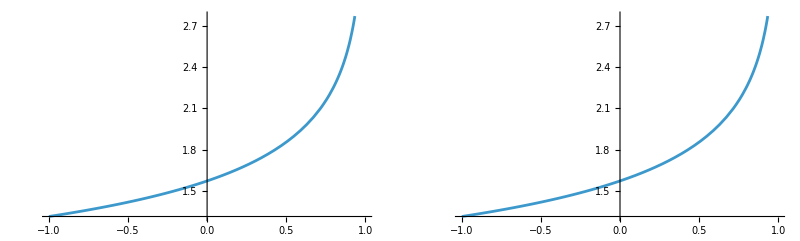

```mathematica
GraphicsGrid[{{Plot[EllipticK[x],{x,-1,1}],Plot[rEllipticK[x],{x,-1,1}]}}]
```

### Complete Elliptic Integral of the Second Kind:

Evaluate $E(0.5)$:

```mathematica
rEllipticE[0.5]
```

## Legendre Incomplete Elliptic Integrals

### Incomplete Elliptic Integral of the Second Kind:

Evaluate $E(1.0, 0.5)$:

```mathematica
rEllipticE[1.0,0.5]
```

### Incomplete Elliptic Integral of the Third Kind:

Note that the argument order is consistent with the built-in EllipticPipaclet:ref/EllipticPihttps://reference.wolfram.com/language/ref/EllipticPi.html ():

```mathematica
rEllipticPi[0.2,1.0,0.5]
```

## Bulirsch Elliptic Integrals

Bulirsch integrals provide high-speed, general representations of complete and incomplete elliptic integrals.

### Complete Integral rCel

Calculate Bulirsch's general complete elliptic integral :

```mathematica
rCel[0.5,0.2,1.0,2.0]
```

### Incomplete Integral rEl1

Evaluate Bulirsch's general incomplete elliptic integral of the first kind :

```mathematica
rEl1[1.0,0.5]
```

## Carlson Symmetric Integrals

Carlson symmetric integrals are highly robust and serve as the foundation of modern elliptic evaluation.

### Carlson $R_F(x, y, z)$

```mathematica
rCarlsonRF[1.0,2.0,3.0]
```

### Error Handling

If invalid inputs are provided, the functions cleanly return Indeterminatepaclet:ref/Indeterminatehttps://reference.wolfram.com/language/ref/Indeterminate.html:

```mathematica
rCarlsonRF[1.0,2.0,-3.0]
```